```mathematica
(*Quit[];*)
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
```

```mathematica
(*Subscript[ϕ^i, 0]*)
ϕ1={};
ϕ2={};
ϕ3={};
ψ1={};
ψ2={};
ψ3={};
dϕ1={};
dϕ2={};
dϕ3={};
dψ1={};
dψ2={};
dψ3={};
(**)
(**)
ϕ1newc=1/(√(2*k))*(1/16+c/(4*π)*(u^(2*k)-1)/(u^(2*k)+1)*logu-1/(8*π^2)*logu^2);
Export[StringJoin["210120_phi1c_k",ToString[k],"_n0.m"],ϕ1newc];
ϕ1new=ϕ1newc/.{c->I};
Export[StringJoin["210120_phi1_k",ToString[k],"_n0.m"],ϕ1new];
ψ2new=ϕ1newc/.{c->-I};
Export[StringJoin["210120_psi2_k",ToString[k],"_n0.m"],ψ2new];
dϕ1new=D[ϕ1new,u]+1/u*D[ϕ1new,logu];
dψ2new=D[ψ2new,u]+1/u*D[ψ2new,logu];
Export[StringJoin["210120_dphi1_k",ToString[k],"_n0.m"],dϕ1new];
Export[StringJoin["210120_dpsi2_k",ToString[k],"_n0.m"],dψ2new];
(**)
(**)
ϕ2newc=1/(√(2*k));
Export[StringJoin["210120_phi2c_k",ToString[k],"_n0.m"],ϕ2newc];
ϕ2new=ϕ2newc/.{c->I};
Export[StringJoin["210120_phi2_k",ToString[k],"_n0.m"],ϕ2new];
ψ1new=ϕ2newc/.{c->-I};
Export[StringJoin["210120_psi1_k",ToString[k],"_n0.m"],ψ1new];
dϕ2new=D[ϕ2new,u]+1/u*D[ϕ2new,logu];
dψ1new=D[ψ1new,u]+1/u*D[ψ1new,logu];
Export[StringJoin["210120_dphi2_k",ToString[k],"_n0.m"],dϕ2new];
Export[StringJoin["210120_dpsi1_k",ToString[k],"_n0.m"],dψ1new];
(**)
(**)
ϕ3newc=1/(√(2*k))*(1/2*(u^(2*k)-1)/(u^(2*k)+1)+c/(2*π)*logu);
Export[StringJoin["210120_phi3c_k",ToString[k],"_n0.m"],ϕ3newc];
ϕ3new=ϕ3newc/.{c->I};
Export[StringJoin["210120_phi3_k",ToString[k],"_n0.m"],ϕ3new];
ψ3new=ϕ3newc/.{c->-I};
Export[StringJoin["210120_psi3_k",ToString[k],"_n0.m"],ψ3new];
dϕ3new=D[ϕ3new,u]+1/u*D[ϕ3new,logu];
dψ3new=D[ψ3new,u]+1/u*D[ψ3new,logu];
Export[StringJoin["210120_dphi3_k",ToString[k],"_n0.m"],dϕ3new];
Export[StringJoin["210120_dpsi3_k",ToString[k],"_n0.m"],dψ3new];
(**)
(**)
ϕ1oldc=ϕ1newc;
ϕ2oldc=ϕ2newc;
ϕ3oldc=ϕ3newc;
(**)
(**)
AppendTo[ϕ1,ϕ1new];
AppendTo[ϕ2,ϕ2new];
AppendTo[ϕ3,ϕ3new];
AppendTo[ψ1,ψ1new];
AppendTo[ψ2,ψ2new];
AppendTo[ψ3,ψ3new];
AppendTo[dϕ1,dϕ1new];
AppendTo[dϕ2,dϕ2new];
AppendTo[dϕ3,dϕ3new];
AppendTo[dψ1,dψ1new];
AppendTo[dψ2,dψ2new];
AppendTo[dψ3,dψ3new];
(**)
(**)
Φlist=CoefficientList[Sum[(-1)^ell*(ϕ1[[ell+1]]*ψ1[[1-1-ell+1]]+ϕ2[[ell+1]]*ψ2[[1-1-ell+1]]+ϕ3[[ell+1]]*ψ3[[1-1-ell+1]]),{ell,0,1-1}],logu];
trρ=k/(2*π)*Sum[(-(2*π*I)^(j+1)/(j+1))*Sum[Residue[(u^(k-1)/(u^(2*k)+1)*Φlist[[j+1]]*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*du])/(2*π*I)]/.{u->Exp[(π*I)/k*(m-1/2)]+du}//ExpandDenominator),{du,0}],{m,1,2*k}]//Together//ExpandDenominator,{j,0,Length[Φlist]-1}];
Export[StringJoin["210120_trrho_k",ToString[k],"_n1.m"],trρ];
```

```mathematica
nmax=20;
```

```mathematica
Table[(
ϕ1listc=(CoefficientList[ϕ1oldc,logu]/.{u->v});
ϕ1newc=Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ1listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)])/.{v->-u+dv}//ExpandDenominator),{dv,0}]+(Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ1listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])])/.{v->Exp[(π*I)/k*(m-1/2)]+dv}//ExpandDenominator),{dv,0}],{m,1,2*k}]//Together//ExpandDenominator),{j,0,Length[ϕ1listc]-1}]//Together//ExpandDenominator;
Export[StringJoin["210120_phi1c_k",ToString[k],"_n",ToString[n],".m"],ϕ1newc];
ϕ1new=ϕ1newc/.{c->I};
Export[StringJoin["210120_phi1_k",ToString[k],"_n",ToString[n],".m"],ϕ1new];
ψ2new=ϕ1newc/.{c->-I};
Export[StringJoin["210120_psi2_k",ToString[k],"_n",ToString[n],".m"],ψ2new];
dϕ1new=D[ϕ1new,u]+1/u*D[ϕ1new,logu];
dψ2new=D[ψ2new,u]+1/u*D[ψ2new,logu];
Export[StringJoin["210120_dphi1_k",ToString[k],"_n",ToString[n],".m"],dϕ1new];
Export[StringJoin["210120_dpsi2_k",ToString[k],"_n",ToString[n],".m"],dψ2new];
(**)
(**)
ϕ2listc=(CoefficientList[ϕ2oldc,logu]/.{u->v});
ϕ2newc=Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ2listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)])/.{v->-u+dv}//ExpandDenominator),{dv,0}]+(Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ2listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])])/.{v->Exp[(π*I)/k*(m-1/2)]+dv}//ExpandDenominator),{dv,0}],{m,1,2*k}]//Together//ExpandDenominator),{j,0,Length[ϕ2listc]-1}]//Together//ExpandDenominator;
Export[StringJoin["210120_phi2c_k",ToString[k],"_n",ToString[n],".m"],ϕ2newc];
ϕ2new=ϕ2newc/.{c->I};
Export[StringJoin["210120_phi2_k",ToString[k],"_n",ToString[n],".m"],ϕ2new];
ψ1new=ϕ2newc/.{c->-I};
Export[StringJoin["210120_psi1_k",ToString[k],"_n",ToString[n],".m"],ψ1new];
dϕ2new=D[ϕ2new,u]+1/u*D[ϕ2new,logu];
dψ1new=D[ψ1new,u]+1/u*D[ψ1new,logu];
Export[StringJoin["210120_dphi2_k",ToString[k],"_n",ToString[n],".m"],dϕ2new];
Export[StringJoin["210120_dpsi1_k",ToString[k],"_n",ToString[n],".m"],dψ1new];
(**)
(**)
ϕ3listc=(CoefficientList[ϕ3oldc,logu]/.{u->v});
ϕ3newc=Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ3listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)])/.{v->-u+dv}//ExpandDenominator),{dv,0}]+(Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ3listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])])/.{v->Exp[(π*I)/k*(m-1/2)]+dv}//ExpandDenominator),{dv,0}],{m,1,2*k}]//Together//ExpandDenominator),{j,0,Length[ϕ3listc]-1}]//Together//ExpandDenominator;
Export[StringJoin["210120_phi3c_k",ToString[k],"_n",ToString[n],".m"],ϕ3newc];
ϕ3new=ϕ3newc/.{c->I};
Export[StringJoin["210120_phi3_k",ToString[k],"_n",ToString[n],".m"],ϕ3new];
ψ3new=ϕ3newc/.{c->-I};
Export[StringJoin["210120_psi3_k",ToString[k],"_n",ToString[n],".m"],ψ3new];
dϕ3new=D[ϕ3new,u]+1/u*D[ϕ3new,logu];
dψ3new=D[ψ3new,u]+1/u*D[ψ3new,logu];
Export[StringJoin["210120_dphi3_k",ToString[k],"_n",ToString[n],".m"],dϕ3new];
Export[StringJoin["210120_dpsi3_k",ToString[k],"_n",ToString[n],".m"],dψ3new];
(**)
(**)
Print[sub["ϕ",StringJoin[ToString[n-1],"→",ToString[n]]],":  ",DateString[]];
(**)
(**)
ϕ1oldc=ϕ1newc;
ϕ2oldc=ϕ2newc;
ϕ3oldc=ϕ3newc;
(**)
(**)
(*#////////////////////////////////////////////////////////////////#*)
(**)
(**)
AppendTo[ϕ1,ϕ1new];
AppendTo[ϕ2,ϕ2new];
AppendTo[ϕ3,ϕ3new];
AppendTo[ψ1,ψ1new];
AppendTo[ψ2,ψ2new];
AppendTo[ψ3,ψ3new];
AppendTo[dϕ1,dϕ1new];
AppendTo[dϕ2,dϕ2new];
AppendTo[dϕ3,dϕ3new];
AppendTo[dψ1,dψ1new];
AppendTo[dψ2,dψ2new];
AppendTo[dψ3,dψ3new];
(**)
(**)
If[OddQ[n+1],
Φlist=CoefficientList[Sum[(-1)^ell*(ϕ1[[ell+1]]*ψ1[[n+1-1-ell+1]]+ϕ2[[ell+1]]*ψ2[[n+1-1-ell+1]]+ϕ3[[ell+1]]*ψ3[[n+1-1-ell+1]]),{ell,0,n+1-1}],logu]//Together;
trρ=k/(2*π)*Sum[(-(2*π*I)^(j+1)/(j+1))*Sum[Residue[(u^(k-1)/(u^(2*k)+1)*Φlist[[j+1]]*BernoulliB[j+1,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*du])]/.{u->Exp[(π*I)/k*(m-1/2)]+du}//ExpandDenominator),{du,0}],{m,1,2*k}]//Together//ExpandDenominator,{j,0,Length[Φlist]-1}];,
(**)
Φprimelist=CoefficientList[Sum[(-1)^ell*1/2*(dϕ1[[ell+1]]*ψ1[[n+1-1-ell+1]]+dϕ2[[ell+1]]*ψ2[[n+1-1-ell+1]]+dϕ3[[ell+1]]*ψ3[[n+1-1-ell+1]]-ϕ1[[ell+1]]*dψ1[[n+1-1-ell+1]]-ϕ2[[ell+1]]*dψ2[[n+1-1-ell+1]]-ϕ3[[ell+1]]*dψ3[[n+1-1-ell+1]]),{ell,0,n+1-1}],logu]//Together;
(*
Φprimelist=CoefficientList[Sum[(-1)^ell*(dϕ1[[ell+1]]*ψ1[[n+1-1-ell+1]]+dϕ2[[ell+1]]*ψ2[[n+1-1-ell+1]]+dϕ3[[ell+1]]*ψ3[[n+1-1-ell+1]]),{ell,0,n+1-1}],logu]//Together;
*)
trρ=k/π*Sum[(-(2*π*I)^(j+1)/(j+1))*Sum[Residue[(u^k/(u^(2*k)+1)*Φprimelist[[j+1]]*BernoulliB[j+1,1/(2*π*I)((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*du])]/.{u->Exp[(π*I)/k*(m-1/2)]+du}//ExpandDenominator),{du,0}],{m,1,2*k}]//Together//ExpandDenominator,{j,0,Length[Φprimelist]-1}];
];
Export[StringJoin["210120_trrho_k",ToString[k],"_n",ToString[n+1],".m"],trρ];
(**)
(**)
Print[super["Trρ",ToString[n+1]],":  ",DateString[]];
),{n,1,nmax}];
```

ϕ_(0→1):  Fri 22 Jan 2021 16:48:15

Trρ^2:  Fri 22 Jan 2021 16:48:16

ϕ_(1→2):  Fri 22 Jan 2021 16:48:21

Trρ^3:  Fri 22 Jan 2021 16:48:22

ϕ_(2→3):  Fri 22 Jan 2021 16:48:48

Trρ^4:  Fri 22 Jan 2021 16:48:56

ϕ_(3→4):  Fri 22 Jan 2021 16:50:47

Trρ^5:  Fri 22 Jan 2021 16:50:54

$Aborted

```mathematica
hoge1=Import["210120_trrho_k1_n1.m"];
hoge2=Import["210120_trrho_k1_n2.m"];
hoge3=Import["210120_trrho_k1_n3.m"];
hoge4=Import["210120_trrho_k1_n4.m"];
hoge5=Import["210120_trrho_k1_n5.m"];
(*hoge6=Import["210120_trrho_k1_n6.m"];
hoge7=Import["210120_trrho_k1_n7.m"];*(
```

```mathematica
hoge1
```

1/32

```mathematica
hoge2//FullSimplify
```

3/2048-1/(96 π^2)

```mathematica
hoge3//FullSimplify
```

-35/524288+11/(15360 π^2)

```mathematica
(**)
-735/67108864+5/(36864 π^4)+2693/(18350080 π^2)
```

```mathematica
hoge4//FullSimplify
```

-105/16777216+323/(5160960 π^2)

```mathematica
hoge5//FullSimplify
```

(30638080-59358336 π^2+5733585 π^4)/(28701118955520 π^4)

```mathematica
(**)
(41390560575+(256 (820019200-9 π^2 (183146496+153901939 π^2)))/π^6)/1215675031250534400
```

```mathematica
hoge6//FullSimplify
```

1/(15689525691076327176834908160000 π^13)(6226426991296512000 ⅈ+π (157925338613141299200+π (387593838101601331200 ⅈ+π (7852672364669317785600+π (-5627449316003512757760 ⅈ+π (-118133009589033644325120+π (13187018925435087532800 ⅈ+π (343558302387605831285760+π (-76787375933713376579648 ⅈ+π (-188060981194679295999296+27 π (-5154619722848004764264 ⅈ+9 π (-1071760050654659469272+2625 π (22611416388991214 ⅈ+44139880743183225 π)))))))))))))

```mathematica
hoge7//FullSimplify
```

-1029279/9007199254740992+17/(275188285440 π^8)+(576531294521262080+4861018564369009152 π^2+1305489943490932995 π^4)/(1596410835477851768094720000 π^6)

```mathematica
N[hoge2]
N[hoge3]
```

0.000263335-0.000245343 ⅈ

2.25795×10^-13

```mathematica
hoge1to7abs={{1,-Log[hoge1]},{2,-Log[Abs[hoge2]]},{3,-Log[hoge3]},{4,-Log[Abs[hoge4]]},{5,-Log[hoge5]},{6,-Log[Abs[hoge6]]},{7,-Log[hoge7]}};hoge1to7odd={{1,-Log[hoge1]},{3,-Log[hoge3]},{5,-Log[hoge5]},{7,-Log[hoge7]}};
```

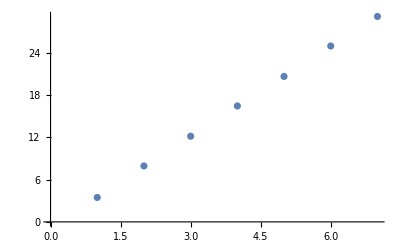

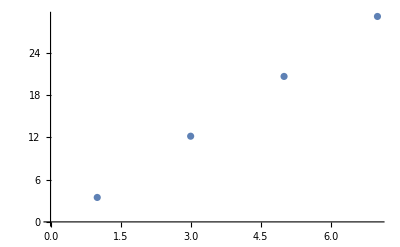

```mathematica
ListPlot[hoge1to7abs,PlotRange->All,AxesOrigin->{0,0}]
ListPlot[hoge1to7odd,PlotRange->All,AxesOrigin->{0,0}]
```